```mathematica
<<peeters`;
peeters`setGitDir["../project/figures/blogit"]
```

/Users/pjoot/project/figures/blogit

```mathematica
<<MaTeX`

(*See MathematicaColorToLatexRGB.nb for color mapping logic.*)
SetOptions[MaTeX,"Preamble"->{"\\usepackage{xcolor,txfonts}","\\definecolor{BlueDarker}{HTML}{0000AA}","\\definecolor{RedDarker}{HTML}{AA0000}","\\definecolor{PurpleDarker}{HTML}{550055}","\\definecolor{OrangeDarker}{HTML}{AA5500}","\\definecolor{GreenDarker}{HTML}{00AA00}"},
"FontSize" -> 16]
```

{BasePreamble→{\usepackage{lmodern,exscale},\usepackage{amsmath,amssymb}},Preamble→{\usepackage{xcolor,txfonts},\definecolor{BlueDarker}{HTML}{0000AA},\definecolor{RedDarker}{HTML}{AA0000},\definecolor{PurpleDarker}{HTML}{550055},\definecolor{OrangeDarker}{HTML}{AA5500},\definecolor{GreenDarker}{HTML}{00AA00}},DisplayStyle→True,ContentPadding→True,LineSpacing→{1.2,0},FontSize→16,Magnification→1,LogFileFunction→None,TeXFileFunction→None}

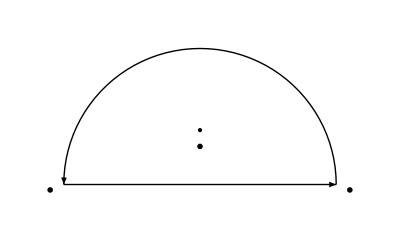

```mathematica
ClearAll[R, lineArrow2, xrange, semicircleArrow, simpleSemicircularContourFig1]
R=5; 
xrange = {{-R,0},{R, 0}};
lineArrow2=Graphics[{
Thick,Arrow[xrange],
Text[MaTeX["-R"], {-1.1 R, -0.2}],
Text[MaTeX["R"], {1.1 R, -0.2}],
Text[MaTeX["z = i"], {0, 1.4}],
PointSize -> Large,
Point[{0,2}]
}];

semicircleArrow[a_, s_]:=Graphics[{Thick,Arrow[Table[{a Cos[t],a Sin[t]},{t,s,s + Pi,Pi/50}]]}]

 simpleSemicircularContourFig1= Show[lineArrow2,semicircleArrow[R, 0],AspectRatio->Automatic,PlotRange->{{-R-1,R+1},{-1,R+1}},Axes->False,Ticks->None,Frame->False]
```

```mathematica
peeters`exportForLatex["simpleSemicircularContourFig1",simpleSemicircularContourFig1]
```

{simpleSemicircularContourFig1.eps,simpleSemicircularContourFig1pn.png}